```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
microsoftdata=Import["C:\\Users\\carte\\OneDrive\\Documents\\Wolfram Mathematica\\Business\\Microsoft.xls"];
```

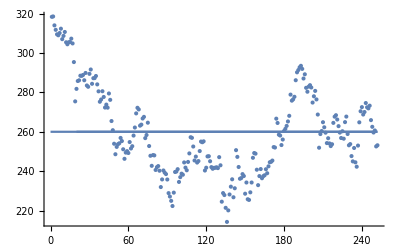

```mathematica
first=Delete[microsoftdata,{1,1}];
new=Partition[Flatten[first],6];
data=Delete[1]/@new;
integers=Table[i,{i,Length[data]}];
For[i=0,i<Length[data],PrependTo[data[[i]], i],i++];
workabledata=Transpose[data];
cutdatax=workabledata[[1]];
cutdatay=workabledata[[2]];
mean=Mean[cutdatay];
stockprices=ListPlot[cutdatay];
Show[Plot[{mean}, {x,0,Length[data]}],Plot[100*(-Exp[-x]*(Sinh[x-20]+0.4))+mean,{x,20,Length[data]}],ListPlot[cutdatay],PlotRange->All]
```

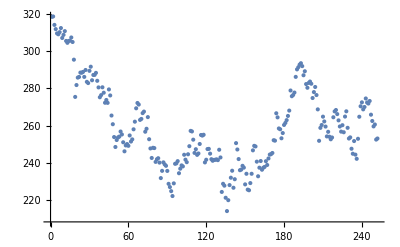

```mathematica
ListPlot[cutdatay]
```

```mathematica
nlm=NonlinearModelFit[cutdatay,Log[a +b x^2+c*x^3+d*x^4+e*x^5+f*x+g*x^6],{a,b,c,d,e,f,g},x]
tsm=TimeSeriesModelFit[cutdatay]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[Log[2.14893×10^22+2.28668×10^22 x+2.59288×10^22 x^2+3.30545×10^22 x^3+5.11×10^22 x^4+8.75886×10^22 x^5+7.9163×10^21 x^6]]

TimeSeriesModel[…]

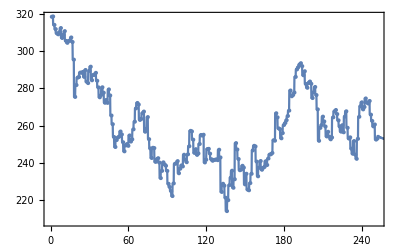

```mathematica
Show[ListPlot[cutdatay],Plot[tsm[x],{x,0,2*Length[data]}],Frame->True]
```

```mathematica
funct=Log[2.1489339089796114*10^22+2.2866808919212725*x*10^22+2.5928817800175734*10^22* x^2+3.3054530870339485*10^22* x^3+5.109999314694549*10^22 *x^4+8.75885688454626*10^22*x^5+7.916300316172018*10^21* x^6];
```

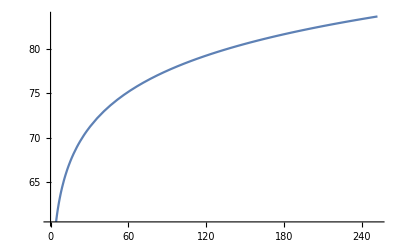

```mathematica
Plot[funct,{x,0,Length[data]}]
```

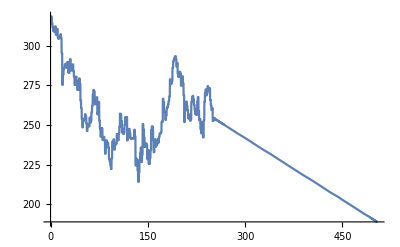

```mathematica
Plot[tsm[x],{x,0,2*Length[data]}]
```

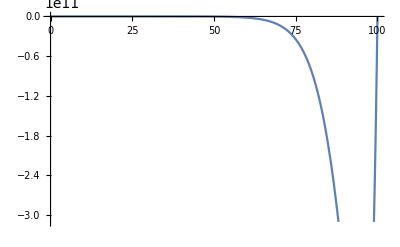

```mathematica
Plot[-Exp[-x]*(Sinh[x]+0.4)*Exp[-x]*(Sinh[x]+0.4)*Exp[-x]*(Sinh[x]+0.5)*(-1/10*x+10)*Exp[1/5*x]*(3*Abs[x])*(2*Abs[x]),{x,0,100}]
```

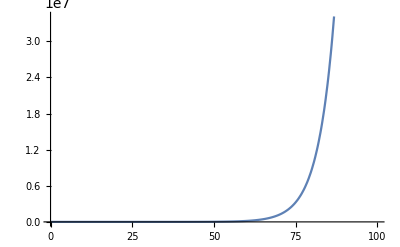

```mathematica
Plot[-Exp[-x]*(Sinh[x]+0.4)+Exp[-x]*(Sinh[x]+0.4)+Exp[-x]*(Sinh[x]+0.5)-1/10*x+10+Exp[1/5*x]+3*Abs[x]+2*Abs[x],{x,0,100}]
```

```mathematica
(Integrate[-Exp[-x]*(Sinh[x]+0.4),{x,0,3}]+Integrate[-1/10*x+10,{x,0,22}]+Integrate[-Exp[-x]*(Sinh[x]+0.4),{x,0,6}]+Integrate[-1/10*x+10,{x,0,20}])/1.18
```

314.424

```mathematica
Integrate[-Exp[-x]*(Sinh[x]+0.4),x]+Integrate[-1/10*x+10,x]+Integrate[-Exp[-x]*(Sinh[x]+0.4),x]+Integrate[-1/10*x+10,x]
```

-0.5 ⅇ^(-2. x)+0.8 ⅇ^(-1. x)+19. x-x^2/10

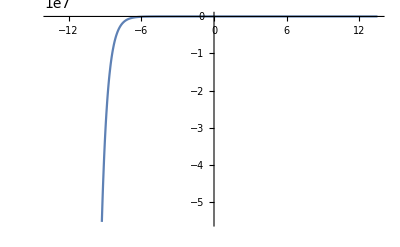

```mathematica
Plot[-0.5 ⅇ^(-2*x)+0.8 ⅇ^-x+19*x-x^2/10,{x,-13.5,13.5}]
```

```mathematica
Plot[Integrate[-Exp[-x]*(Sinh[x]+0.4),{x,20,23}]+Integrate[-1/10*x+10,{x,25,47}]+Integrate[-Exp[-x]*(Sinh[x]+0.4),{x,47,53}]+Integrate[-1/10*x+10,{x,0,20}],{x,0,53}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {0.00108271,20,23}.

Integrate::ilim: Invalid integration variable or limit(s) in {0.00108271,25,47}.

Integrate::ilim: Invalid integration variable or limit(s) in {0.00108271,47,53}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

NIntegrate::itraw: Raw object 0.00108271 cannot be used as an iterator.

General::stop: Further output of NIntegrate::itraw will be suppressed during this calculation.

-Graphics-

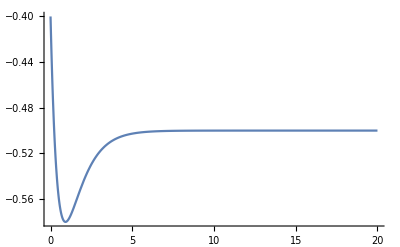

```mathematica
Plot[-Exp[-x]*(Sinh[x]+0.4),{x,0,20},PlotRange->All]
```

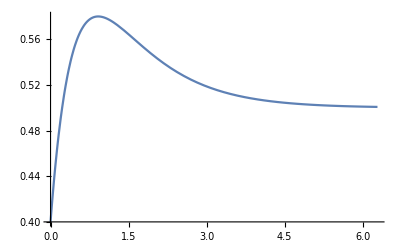

```mathematica
Plot[Exp[-x]*(Sinh[x]+0.4),{x,0,2*Pi},PlotRange->All]
```

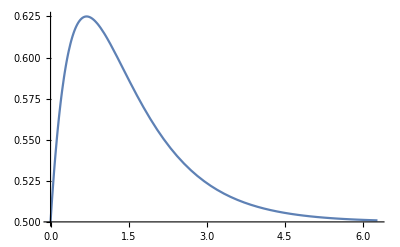

```mathematica
Plot[Exp[-x]*(Sinh[x]+0.5),{x,0,2*Pi},PlotRange->All]
```

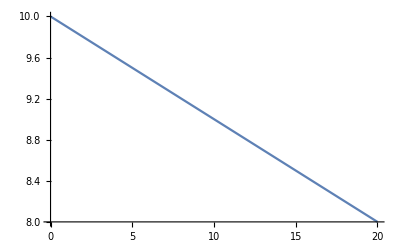

```mathematica
Plot[-1/10*x+10,{x,0,20},PlotRange->All]
```

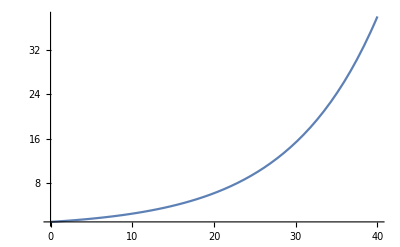

```mathematica
Plot[Exp[1/11*x],{x,0,40},PlotRange->All]
```

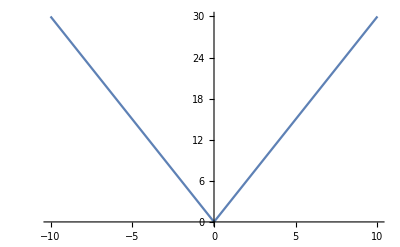

```mathematica
Plot[3*Abs[x],{x,-10,10},PlotRange->All]
```

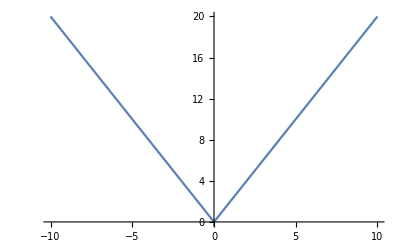

```mathematica
Plot[2*Abs[x],{x,-10,10},PlotRange->All]
```